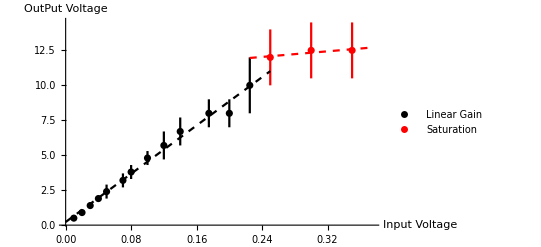

```mathematica
Needs["ErrorBarPlots`"]
Data={{0.01, .5}, {.05, 2.4}, {.07, 3.2}, {.04, 1.9}, {.03, 1.4}, {.02, .9}, {.08, 3.8}, {.1, 4.8}, {.12, 5.7}, {.14, 6.7}, {.2, 8}, {.225, 10}, {.175, 8}};
SatData = {{.25, 12}, {.3, 12.5}, {.35, 12.5}};

model1=LinearModelFit[Data,x,x];
model2=LinearModelFit[SatData, x, x];

L1=ErrorListPlot[{{{0.01, .5}, ErrorBar[.2]}, {{.05, 2.4}, ErrorBar[.5]}, {{.07, 3.2}, ErrorBar[.5]}, {{.04, 1.9}, ErrorBar[.2]}, {{.03, 1.4}, ErrorBar[.2]}, {{.02, .9}, ErrorBar[.2]}, {{.08, 3.8}, ErrorBar[.5]}, {{.1, 4.8}, ErrorBar[.5]}, {{.12, 5.7}, ErrorBar[1]}, {{.14, 6.7}, ErrorBar[1]}, {{.2, 8}, ErrorBar[1]}, {{.225, 10}, ErrorBar[2]}, {{.175, 8}, ErrorBar[1]}},
 PlotStyle->{Black}, PlotLegends->{"Linear Gain"}];
L2=ErrorListPlot[{{{.25, 12}, ErrorBar[2]}, {{.3, 12.5}, ErrorBar[2]}, {{.35, 12.5}, ErrorBar[2]}}, PlotStyle->{Red}, PlotLegends->{"Saturation"}];

P1=Plot[model1[x], {x, 0, .25}, PlotStyle->{Black, Dashed}];
P2=Plot[model2[x], {x,.225,.375}, PlotStyle->{Red, Dashed}];

Show[L1, L2,P1, P2, PlotRange->All, AxesLabel->{Style["Input Voltage", FontSize->14], Style["OutPut Voltage", FontSize->14]}, FrameTicks->{Large}]
```